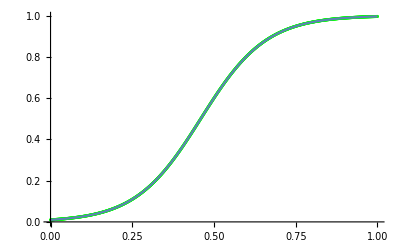

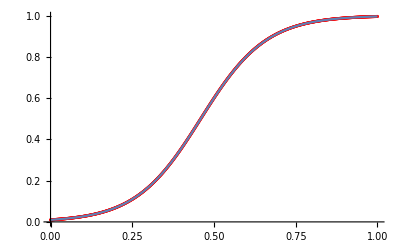

Time used by 1000 RK4:

$Aborted

Time used by 1000 AB4:

$Aborted

```mathematica
(*RK от упр 4*)
RK4[f_,t0_,T_,u0_,h_]:=(
p1=1/6;
p2=1/3;
p3=1/3;
p4=1/6;

n=Ceiling[(T-t0)/h];
tc=t0;
uc=u0;
res=Table[0,n+1];
res[[1]]=u0;

For[k=1,k≤n,k++,

k1=h*f[tc,uc];
k2=h*f[tc+1/2*h,uc+1/2*k1];
k3=h*f[tc+1/2*h,uc+1/2*k2];
k4=h*f[tc+h,uc+k3];

res[[k+1]]=res[[k]]+p1*k1+p2*k2+p3*k3+p4*k4;
tc=tc+h;
uc=res[[k+1]];
];

res)


(*Задача 1*)

AB4[f_,t0_,T_,u0_,h_]:=(
n2=Ceiling[(T-t0)/h];
res2=Table[0,n2+1];
RKapprox=RK4[f,t0,t0+3*h,u0,h];
For[it=1,it≤4,it++,res2[[it]]=RKapprox[[it]]];

m=4;
tc2=t0+3*h;
uc2=res2[[m]];
func=Table[f[t0+kk*h,res2[[kk+1]]],{kk,0,3}];
coeffs=List[-3/8,37/24,-59/24,55/24];

While[T>tc2,
uc2=uc2+h*func.coeffs;

m=m+1;
res2[[m]]=uc2;
tc2=tc2+h;

func=RotateLeft[func,1];
func[[4]]=f[tc2,uc2];
];

res2
)

(*Задача 2*)

f[t_,u_]:=10*u*(1-u);
ur[t_]:=0.01/(0.01+0.99*Exp[-10*t]);
T=1;
t0=0;
u0=0.01;
h=0.001;

(*Коректност*)

yRK=RK4[f,t0,T,u0,h];
yAB=AB4[f,t0,T,u0,h];
n=Length[yRK];
nAB=Length[yAB];
x=Table[t0+k*h,{k,0,n-1}];
xAB=Table[t0+k*h,{k,0,nAB-1}];
runge=ListPlot[Table[{x[[k]],yRK[[k]]},{k,1,n}],PlotStyle->Green];
adams=ListPlot[Table[{xAB[[k]],yAB[[k]]},{k,1,nAB}],PlotStyle->Red];
actual=Plot[ur[t],{t,0,1}];
Show[runge,actual]
Show[adams,actual]


(*Времена*)

Print["Time used by 1000 RK4:"]
Timing[For[k2=1,k2≤1000,k2++,
ytRK2=RK4[f,t0,T,u0,h];
];][[1]]

Print["Time used by 1000 AB4:"]
Timing[For[k3=1,k3≤1000,k3++,
ytAB2=AB4[f,t0,T,u0,h];
];][[1]]
```